```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

## Projections onto L2(-1,1)

```mathematica
Integrand[x]:=Piecewise[{{Abs[x],x<0},{0,x≥0}}];
TestPoints=15;
```

### Integral of a function using Gauss Lengendre quadrature points

```mathematica
(*Integrates a functions f from xl to xr*)
GaussIntegrate[f_,xl_,xr_,n_]:=Module[{GaussPoints,result},
GaussPoints = GaussianQuadratureWeights[n,xl,xr];

result = 0;
Do[result=result+(f/.x->GaussPoints⟦ii,1⟧)*GaussPoints⟦ii,2⟧,{ii,1,Length[GaussPoints]}];
result
]
```

#### Convergence Study

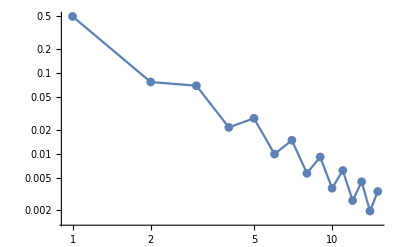

```mathematica
TrueValue = Integrate[Integrand[x],{x,-1,1}];
NumericalValue = Flatten[ConstantArray[0,{1,TestPoints}]];
ErrorValue = Flatten[ConstantArray[0,{1,TestPoints}]];

Do[NumericalValue⟦ii⟧=GaussIntegrate[Integrand[x],-1,1,ii];ErrorValue⟦ii⟧=Abs[TrueValue-NumericalValue⟦ii⟧];,{ii,1,TestPoints}];

ListLogLogPlot[ErrorValue,Joined->True,PlotMarkers->Automatic]
```

```mathematica
?Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

### Projection using Legendre Polynomials

```mathematica
(*Project an L2 function using Legendre polynomials between -1 to 1.
Projection using Gauss Legendre Quadrature*)
```

```mathematica
ProjectLegendreNumerical[f_,n_]:=Module[{Projection,coeff,basis},
Projection =0;
Do[
coeff = GaussIntegrate[f*LegendreP[ii-1,x],-1,1,20];
Projection = Projection + coeff*LegendreP[ii-1,x]/Integrate[LegendreP[ii-1,x]^2,{x,-1,1}];,{ii,1,n}];
Chop[Simplify[Projection]]
]

(*Projection using Exact Integration*)
ProjectLegendreExact[f_,n_]:=Module[{Projection,coeff,basis},
Projection =0;
Do[
coeff = Integrate[f*LegendreP[ii-1,x],{x,-1,1}];
Projection = Projection + coeff*LegendreP[ii-1,x]/Integrate[LegendreP[ii-1,x]^2,{x,-1,1}];,{ii,1,n}];
Chop[Simplify[Projection]]
]
```

#### Convergence Test

```mathematica
NumericalValue = Flatten[ConstantArray[0,{1,TestPoints}]];
NumericalValueExactIntegral = Flatten[ConstantArray[0,{1,TestPoints}]];
ErrorValue = Flatten[ConstantArray[0,{1,TestPoints}]];
ErrorValueExactIntegral=Flatten[ConstantArray[0,{1,TestPoints}]];

Do[NumericalValue⟦ii⟧=ProjectLegendreNumerical[Integrand[x],ii];
NumericalValueExactIntegral⟦ii⟧=ProjectLegendreExact[Integrand[x],ii];ErrorValue⟦ii⟧=Sqrt[Integrate[(Integrand[x]-NumericalValue⟦ii⟧)^2,{x,-1,1}]];
ErrorValueExactIntegral⟦ii⟧=Sqrt[Integrate[(Integrand[x]-NumericalValueExactIntegral⟦ii⟧)^2,{x,-1,1}]];,{ii,1,TestPoints}];
```

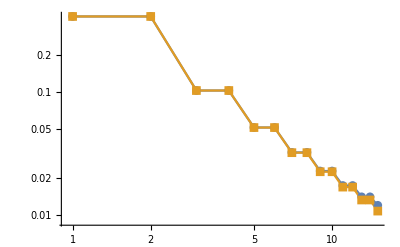

```mathematica
ListLogLogPlot[{ErrorValue,ErrorValueExactIntegral},Joined->True,PlotMarkers->Automatic]
```

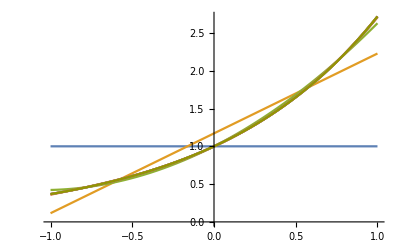

```mathematica
Plot[{NumericalValue},{x,-1,1}]
```

```mathematica
?Piecewise
```

Piecewise[{{val_1,cond_1},{val_2,cond_2},…}] represents a piecewise function with values val_i in the regions defined by the conditions cond_i. 
Piecewise[{{val_1,cond_1},…},val] uses default value val if none of the cond_i apply. The default for val is 0.